```mathematica
Remove["Global`*"];
Unprotect[In,Out];
Clear[In,Out];
Off[General::spell1]
```

```mathematica
data=ReadList["functf.dat",Number,RecordLists->True];
nOfFs=7;
radialCoord=ReadList["gridx.dat",Number];
angularCoord=ReadList["gridy.dat",Number];
nx=Length[radialCoord];
ny=Length[angularCoord];
```

```mathematica
dat=ArrayReshape[data,{nx ny,nOfFs}];
```

```mathematica
(*1 2 3 4 5 6 7*)(*nr,w,alpha,c1,c2,c3,rh*)
conf=ReadList["res.txt",{Number,Number,Number,Number,Number,Number,Number}];

nr=conf[[1]][[1]];
V0=conf[[1]][[2]];
wf=conf[[1]][[3]];
rh=conf[[1]][[4]];

Xtor[X_]:=If[X≠1,Sqrt[(X/(1-X))^2],1000]
f1=Table[{radialCoord[[j]],angularCoord[[i]],dat[[j+(i-1)*nx,1]]},{i,1,ny},{j,1,nx}];
f2=Table[{radialCoord[[j]],angularCoord[[i]],dat[[j+(i-1)*nx,2]]},{i,1,ny},{j,1,nx}];
f0=Table[{radialCoord[[j]],angularCoord[[i]],dat[[j+(i-1)*nx,3]]},{i,1,ny},{j,1,nx}];
Z=Table[{radialCoord[[j]],angularCoord[[i]],dat[[j+(i-1)*nx,4]]},{i,1,ny},{j,1,nx}];
W=Table[{radialCoord[[j]],angularCoord[[i]],dat[[j+(i-1)*nx,5]]},{i,1,ny},{j,1,nx}];
if1=Interpolation[Flatten[f1,1],InterpolationOrder->4];
if2=Interpolation[Flatten[f2,1],InterpolationOrder->4];
if0=Interpolation[Flatten[f0,1],InterpolationOrder->4];
iZ=Interpolation[Flatten[Z,1],InterpolationOrder->4];
iW=Interpolation[Flatten[W,1],InterpolationOrder->4];
f1=if1;
f2=if2;
f0=if0;
Z=iZ;
W=iW;
```

```mathematica
derVplus[r_,t_]=-((2 W[r, t]g'[r] + (E^(f0[r, t] - f2[r, t])Csc[t] (-2 r H[r] g'[r]+g[r] (r H'[r]+2 H[r](1+r D[f0[r, t],r] - r D[f2[r, t],r]))))/Sqrt[H[r]] - 2 g[r] D[W[r, t],r])/(2 g[r]^2));
derVminus[r_,t_]=(-2 W[r, t] g'[r]+( E^(f0[r, t] - f2[r, t])Csc[t] (-2 r H[r]g'[r]+g[r] (r H'[r]+2 H[r] (1 + r D[f0[r, t],r] - r D[f2[r, t],r]))))/Sqrt[H[r]] + 2 g[r] D[W[r, t],r])/(2 g[r]^2);
```

```mathematica
g[r_] := r^2+rh^2;
H[r_] := 1 - rh/r;
```

```mathematica
findRoots[f_,xMax_]:=Block[{zeros,soln,y,x},
zeros=Reap[soln=y[x]/.First[NDSolve[{y'[x]==Evaluate[D[f[x],x]],y[xMax]==(f[xMax])},y[x],{x,xMax,10^-16},Method->{"EventLocator","Event"->y[x],"EventAction":>Sow[{x,y[x]}]}]]][[2,1]];
{Plot[f[x],{x,rh,xMax},Epilog->{PointSize[Medium],Red,Point[zeros]}],zeros[[All,1]],soln}]
```

```mathematica
derVplusEq[r_]=derVplus[r,π/2];
derVminusEq[r_]=derVminus[r,π/2];
```

NDSolve::ndsz: At x == 0.1, step size is effectively zero; singularity or stiff system suspected.

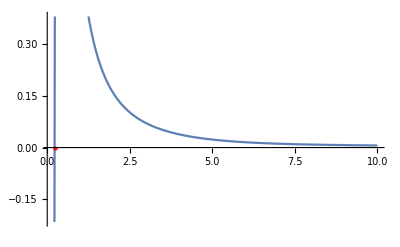
{-Graphics-,{0.222468},InterpolatingFunction[{{0.1, 10.}}, <>][x]}

NDSolve::ndsz: At x == 0.1, step size is effectively zero; singularity or stiff system suspected.

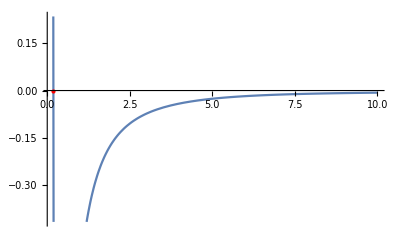
{-Graphics-,{0.18645},InterpolatingFunction[{{0.1, 10.}}, <>][x]}

```mathematica
{dVplusPlot,dVplusRoots,sol1}=findRoots[derVplusEq,10]
{dVminusPlot,dVminusRoots,sol2}=findRoots[derVminusEq,10]
```